```mathematica
Manuel de la Cruz González DNI:70909708H
```

```mathematica
ENTREGA 1
```

```mathematica
PROBLEMA 1:
f[x_]:=Exp[-x]*Sin[1-x^2]*(1-x^2)
```

```mathematica
Function[x,Exp[-x] Sin[1-x^2] (1-x^2)]
```

Function[x,Exp[-x] Sin[1-x^2] (1-x^2)]

```mathematica
Plot[f[x],{x,1.5,2.5}]
```

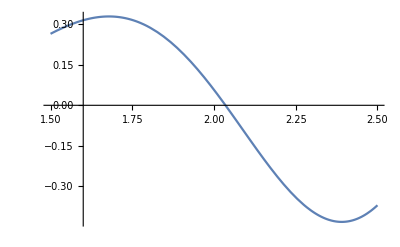

```mathematica
FindRoot[f[x],{x,1.5,2.5}]
```

```mathematica
{x->2.035090330572526}
```

{x→2.03509}

```mathematica
Valor obtenido con nuestro programa de la bisección para una precisión de 10^-5en el intervalo [1.5,2.5]
```

```mathematica
2.03508758545
```

2.03509

```mathematica
Número de iteraciones:
```

```mathematica
16
```

```mathematica
PROBLEMA 2:
```

```mathematica
Mediante el método de Newton comenzando en 1.8 y para una sensibilidad de 10^-5, el resultado obtenido ha sido:
```

```mathematica
2.0350903306
```

2.03509

```mathematica
Número de iteraciones:
```

```mathematica
5
```

```mathematica
PROBLEMA 3:
```

```mathematica
El resultado obtenido con el método de la secante para el intervalo [1.5,2.5] y una precisión de 10^-5:
```

```mathematica
2.03509033054
```

2.03509

```mathematica
Número de iteraciones:
```

```mathematica
6
```

```mathematica
PROBLEMA 4:
```

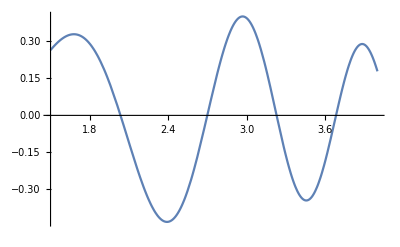

```mathematica
Plot[f[x],{x,1.5,4.0}]
```

```mathematica
FindRoot[f[x]==0,{x,2}]
```

{x→2.03509}

```mathematica
FindRoot[f[x]==0,{x,2.6}]
```

{x→2.69874}

```mathematica
FindRoot[f[x]==0,{x,3.2}]
```

{x→3.22874}

```mathematica
FindRoot[f[x]==0,{x,3.6}]
```

{x→3.68326}

```mathematica
Las raíces obtenidas con nuestro programa para el intervalo [1.5,4.0]con una precisión de 10^-5 han sido:
```

```mathematica
2.03508911133
```

2.03509

```mathematica
2.69873657227
```

2.69874

```mathematica
3.22874145508
```

3.22874

```mathematica
3.68325805664
```

3.68326

```mathematica
El número de iteraciones en todas ha sido de:
```

```mathematica
11
```

```mathematica
Los valores de nuestro programa coinciden con los de mathematica por lo que podemos suponer que funciona bien.
```

```mathematica
---MÁXIMOS Y MÍNIMOS---
```

```mathematica
FindMaximum[f[x],{x,1.5}]
```

{0.328958,{x→1.67865}}

```mathematica
FindMinimum[f[x],{x,2.3}]
```

{-0.431771,{x→2.39067}}

```mathematica
FindMaximum[f[x],{x,2.8}]
```

{0.401029,{x→2.96877}}

```mathematica
FindMinimum[f[x],{x,3}]
```

{-0.344884,{x→3.45577}}

```mathematica
FindMaximum[f[x],{x,3.7}]
```

{0.289333,{x→3.88323}}

```mathematica
Los máximos encontrados con nuestro programa han sido:
```

```mathematica
0.328766, en x=1.6875
```

```mathematica
0.400749, en x=2.9625
```

```mathematica
0.289173, en x=3.8875
```

```mathematica
Los mínimos encontrados han sido:
```

```mathematica
-0.4317195, en x=2.3875
```

```mathematica
-0.344086, en x=3.4625
```

```mathematica
Los resultados de mathematica y de nuestro programa coinciden por lo que podemos suponer que el programa funciona correctamente.
```